### Drag Racer Revisited

In the first drag racer worksheet, I gave you a graph of the position as a function of time, and a table of the positions for each half-second. From those you got the velocity, and the acceleration.

The basic formula you used to get the velocity was

v(t_i)=(x(t_(i+1))-x(t_i))/(t_(i+1)-t_i)

And the basic formula you used to get the acceleration was

a(t_i)=(v(t_(i+1))-v(t_i))/(t_(i+1)-t_i)

It is important to note that these are approximations to the instantaneous velocity and the instantaneous acceleration. We didn’t take a limit that t_(i+1)-t_i→0. We just used the time steps in the table, which were 0.5 apart.

### Velocity from Acceleration!?

Summarizing, Step 1, we got the velocity from the position. Then, Step 2, we got the acceleration from the velocity. Can this process be reversed!?

More specifically from the second step of the process, acceleration from velocity, can we reverse the second step and get velocity from acceleration? Sure as heck we can! Just rearrange this formula:

a(t_i)=(v(t_(i+1))-v(t_i))/(t_(i+1)-t_i)

v(t_(i+1))=v(t_i)+(t_(i+1)-t_i)*a(t_i)

That’s the reversal we are looking for. Let’s make the notation a little simpler. We’ll write that as

v_(i+1)=v_i+Δt*a_i

Let’s also write it out for a few values of i:

v_1=v_0+Δt*a_o
v_2=v_1+Δt*a_1
v_3=v_2+Δt*a_2

You could even substitute in and get an equivalent equation for v_3 that did not depend on v_2.

v_3=v_1+Δt*a_1+Δt*a_2

And substitute again:

v_3=v_0+Δt*a_o+Δt*a_1+Δt*a_2

Now you can see the pattern, perhaps:

v_(n+1)=v_0+∑_(i=0)^n Δt*a_i

So to summarize, we can get the velocities from the accelerations. However, it seems that there is no escaping that we need to know the initial velocity. In our drag racer problem, the initial velocity was zero, so that makes finding the later velocities pretty straightforward.

### Position from Velocity?

Well, we got all the velocities from the initial velocity and the accelerations.

It stands to reason that we can finish undoing the process that we set out to undo by also undoing the first step, which was getting the velocities from the positions.

We start with

v(t_i)=(x(t_(i+1))-x(t_i))/(t_(i+1)-t_i)

and rearrange it to get

x(t_(i+1))=x(t_i)+(t_(i+1)-t_i)*v(t_i)

That’s the reversal we are looking for. Or more compactly:

x_(i+1)=x_i+Δt*v_i

We can write that out for a few values of i:

x_1=x_0+Δt*v_o
x_2=x_1+Δt*v_1
x_3=x_2+Δt*v_2

We can do the substitutions and see that we can the position at any time:

x_(n+1)=x_0+∑_(i=0)^n Δt*v_i

So to summarize, we can get the positions from the velocities. There is no escaping that we need to know initial position. In our drag racer problem, we can declare that the initial position while the drag racer waits for the green light will be zero.

### Putting it into Practice

```mathematica
acceleration[t_]:= Piecewise[{{0,t<5},{6, t≥5 && t<10}, {0, t⩾10}}]
```

Here is a plot of the drag racer’s acceleration from t=4, to t=12.

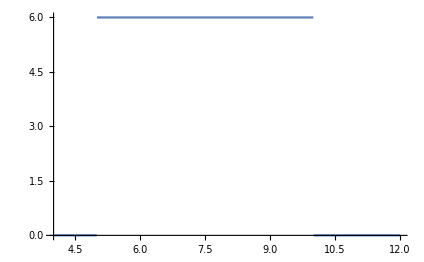

```mathematica
Plot[acceleration[t],{t,4,12}]
```

As you can see, the drag racer is on the gas and accelerating at “6” from t=5 to t=10, and otherwise at rest or coasting (no acceleration).

I put “6” in quotes, because we haven’t really talked about the units much. In most science problems, distance is measured in meters, time is measured in seconds, and from the definition of the derivative (and the derivative of the derivative), you can see that acceleration would then be measured in meters/seconds^2. By the way, 6 meters/second^2 is about 60% of the acceleration of gravity. An extremely high performance drag racer can actually do many times that.

Here is a table of the accelerations of the drag racer from t=0 to t=12.

```mathematica
tableOfValues=Table[{t, acceleration[t], "        ", "        "}, {t,0, 12, 0.5}];
```

```mathematica
Grid[Prepend[tableOfValues, {"time", "acceleration", "   velocity   ", "  position  "}], Frame->All]
```

time | acceleration |    velocity    |   position  
0. | 0 |          |         
0.5 | 0 |          |         
1. | 0 |          |         
1.5 | 0 |          |         
2. | 0 |          |         
2.5 | 0 |          |         
3. | 0 |          |         
3.5 | 0 |          |         
4. | 0 |          |         
4.5 | 0 |          |         
5. | 6 |          |         
5.5 | 6 |          |         
6. | 6 |          |         
6.5 | 6 |          |         
7. | 6 |          |         
7.5 | 6 |          |         
8. | 6 |          |         
8.5 | 6 |          |         
9. | 6 |          |         
9.5 | 6 |          |         
10. | 0 |          |         
10.5 | 0 |          |         
11. | 0 |          |         
11.5 | 0 |          |         
12. | 0 |          |

Fill in the third column of this table with approximations to the velocity.

The formula you will be using for this is

v_(i+1)=v_i+Δt*a_i

For example:

v_4.5=v_4.0+0.5*a_4.0

### Plotting Velocity

On the next page is a place to plot the velocities you found.

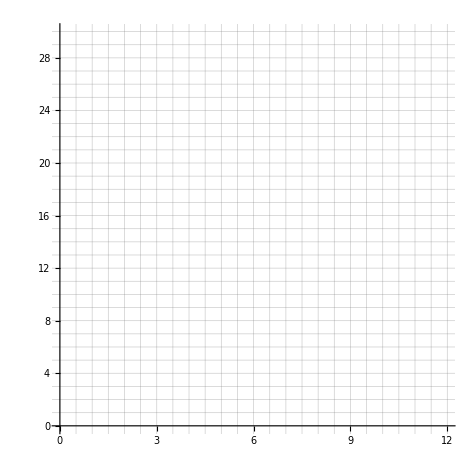

```mathematica
Plot[{}, {t, 0, 12}, PlotRange->{{0, 12},{0, 30}}, GridLines->{Range[0,12, 0.5], Range[0, 30, 1]}, Ticks->{Range[0, 12, 1], Automatic}, AspectRatio->1]
```

### Plotting Position

Now that you have filled in the third column of the table, fill in the fourth column with approximations to the position.

The formula you will be using for this is

x_(i+1)=x_i+Δt*v_i

Once you have done that, on the next page is a place to plot the positions you found.

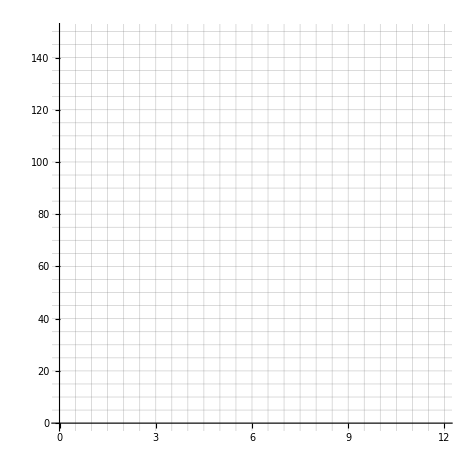

```mathematica
Plot[{}, {t, 0, 12}, PlotRange->{{0, 12},{0, 150}}, GridLines->{Range[0,12, 0.5], Range[0, 150, 5]}, Ticks->{Range[0, 12, 1], Automatic}, AspectRatio->1]
```

### In Summary

On the previous drag racer worksheet, you did a numerical approximation to the derivative and the second derivative.

You have found that this process can be undone. If you have the second derivative, you can get the first derivative, and if you have the first derivative, you can get the original function (you needed the initial condition though, at t=0).

A good name for undoing the derivative might be the undo-derivative. In fact, some people call it the anti-derivative. More commonly it is called the “integral.”

Although we have introduced no theory for integration (that doesn’t come in Spivak until Chapter 13), you have seen what the numerical approximation to the integral looks like, and I am hopeful that this increases your intuition whenever you actually encounter the theory of integrals.